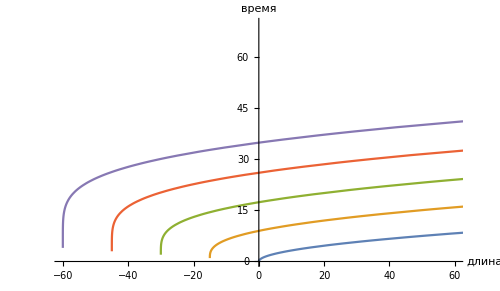

```mathematica
dx0=60;
x0 = 0;
τ = 1;
tt= 40;
dStart = 0.122;
λ= 15;
tmax =120;


Subscript[V, max] =40;
vm=0;
a=2;
q =1;
qq=1;

R[t_] := If[t <= tt, 1,0];
Manipulate[
Module[{solF, solS, solT, u,  v,  w, t},

solF= NDSolve[{u''[t]== R[t]*a*(1-u'[t]/(Subscript[V, max]))+(1-R[t])*(vm-u'[t])/q, u[t /; t≤ 0] == -0*λ, u'[t /; t≤ 0] == 0},u,{t,0 ,tmax}];
solS = NDSolve[{v'[t]==dStart* (Evaluate[u[t-τ] /.solF][[1]]-v[t]-λ), v[t /; t≤ τ ] == -1*λ},v,{t,τ,tmax}];
solT = NDSolve[{w'[t]== dStart* (Evaluate[v[t-τ] /.solS][[1]]-w[t]-λ), w[t /; t≤ 2*τ ] == -2*λ},w,{t,2*τ  ,tmax}];
sol4 = NDSolve[{p'[t]==dStart* (Evaluate[w[t-τ] /.solT][[1]]-p[t]-λ), p[t /; t≤ 3*τ ] == -3*λ},p,{t,3*τ  ,tmax}];
sol5 = NDSolve[{g'[t]==dStart* (Evaluate[p[t-τ] /.sol4][[1]]-g[t]-λ), g[t /; t≤ 4*τ ] == -4*λ},g,{t,4*τ  ,tmax}];
ParametricPlot[{Evaluate[{t-4*τ,u'[t-4*τ]} /. solF],Evaluate[{t-3*τ,v'[t-3*τ]} /. solS],Evaluate[{t-2*τ,w'[t-2*τ]} /. solT],Evaluate[{t-τ,p'[t-τ]} /. sol4],Evaluate[{t,g'[t]} /. sol5]},{t,4*τ,tmax}, PlotRange->{{0,100},{0,50}},AxesLabel->{время,скорость},PlotLegends->Placed[{"машина №1","машина №2","машина №3","машина №4","машина №5"},{Right,Center}],ImageSize->500]]
,{{λ,λStart},0,30,1},{{a,2},0,15,1},{{q,1},0,15,1},{{τ,1},0,3,1},{{dStart,1},0,10,1}]

Module[{solF, solS, solT, u,  v,  w, t},

solF= NDSolve[{u''[t]== R[t]*a*(1-u'[t]/(Subscript[V, max]))+(1-R[t])*(vm-u'[t])/q, u[t /; t≤ 0] == -0*λ, u'[t /; t≤ 0] == 0},u,{t,0 ,tmax}];
solS = NDSolve[{v'[t]==dStart* (Evaluate[u[t-τ] /.solF][[1]]-v[t]-λ), v[t /; t≤ τ ] == -1*λ},v,{t,τ,tmax}];
solT = NDSolve[{w'[t]== dStart* (Evaluate[v[t-τ] /.solS][[1]]-w[t]-λ), w[t /; t≤ 2*τ ] == -2*λ},w,{t,2*τ  ,tmax}];
sol4 = NDSolve[{p'[t]==dStart* (Evaluate[w[t-τ] /.solT][[1]]-p[t]-λ), p[t /; t≤ 3*τ ] == -3*λ},p,{t,3*τ  ,tmax}];
sol5 = NDSolve[{g'[t]==dStart* (Evaluate[p[t-τ] /.sol4][[1]]-g[t]-λ), g[t /; t≤ 4*τ ] == -4*λ},g,{t,4*τ  ,tmax}];
ParametricPlot[{Evaluate[{u[t-4*τ],t-4*τ} /. solF],Evaluate[{v[t-3*τ],t-3*τ} /. solS],Evaluate[{w[t-2*τ],t-2*τ} /. solT],Evaluate[{p[t-τ],t-τ} /. sol4],Evaluate[{g[t],t} /. sol5]},{t,4*τ,tmax}, PlotRange->{{-60,60},{0,70}},AxesLabel->{длина,время}]]
```